# Using Simple pendulum for measuring g

## And the theortical error

```mathematica
(* The equation of motion for pendulum *)
Ι θ''[t]==-M g l Sin[θ[t]]
(* where 
I = momemt of inertia
M = Mass
g = gravitational constant
l = lenght from the pivot and center of mass *)
```

```mathematica
(* for small occilation *)
```

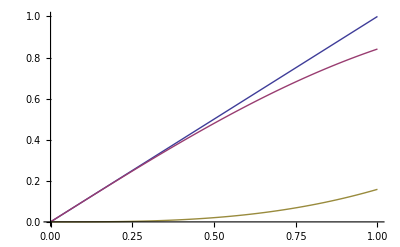

```mathematica
Plot[{θ,Sin[θ],θ-Sin[θ]},{θ,0,1}]
```

```mathematica
θ''[t]≈-(M g l)/Ι θ[t]
Ω^2=(M g l)/Ι
g =(Ω^2 Ι)/(M l)
```

```mathematica
δg=2 Ω Ι/(M l)δΩ+Ω^2/(M l)δΙ-(Ω^2 Ι)/(M^2 l)δM-(Ω^2 Ι)/(M l^2)δl
δg/g=2 1/Ω δΩ+ 1/Ι δΙ-1/M δM-1/l δl
```

```mathematica
Δg/g=√(2(ΔΩ/Ω)^2+(ΔΙ/Ι)^2+(ΔM/M)^2+(Δl/l)^2)
```

```mathematica
(* in fact, Ι depends on M and l, thus, there are covariant*)
```

```mathematica
(* for simple pedulum *)
```

```mathematica
∫_0^(2π) ∫_0^π ∫_0^a ρ r^2 r^2 Sin[θ]ⅆrⅆθⅆϕ/.ρ-> M/(4/3 π a^3)
```

(3 a^2 M)/5

```mathematica
Subscript[Ι, S]=3/5 a^2 M+M l^2;
Subscript[Ι, rod]=1/12 m l^2;
Subscript[Ι, T]=Subscript[Ι, S]+Subscript[Ι, rod];
```

```mathematica
Clear[Ι]
```

```mathematica
(* for a 0.5 kg sphere and m = 0.01 kg rope, wiht 1 meter length *)
M=0.5;
m=0.01;
a=0.1;
l=1;
Subscript[Ι, S]
Subscript[Ι, rod]
```

0.503

0.000833333

```mathematica
(* If we neglect the rope *)
```